## Logistic Map Bifurcation Diagram F. I. Giasemis

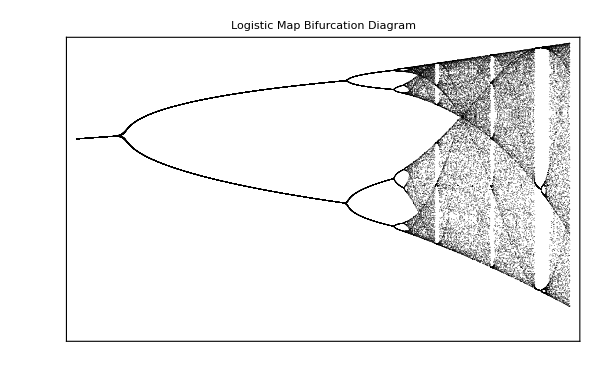

```mathematica
r=2.9;
bif={};
For[j=1,j<1000,j++;
r=r+.001;
x=.5;
For[i=1,i<200,i++;
x=r*x*(1-x);
]
For[i=1,i<100,i++;
AppendTo[bif,x];
x=r*x*(1-x);
]
]
ListPlot[bif,Frame->True,Axes->False, FrameTicks->False,PlotLabel->"Logistic Map Bifurcation Diagram",PlotStyle->{Black,PointSize[0.0001]}]
```